```mathematica
f[M_?NumericQ,m_,L_,z_, z0Val_]:=6 (-M/(3 m)+(2 L^(5/2))/(3 Sqrt[3] m^(3/2)) ArcTanh[(Sqrt[3] Sqrt[m] M)/(2 L^(5/2))])-z+z0Val;

mVal=1.0;
z0Val=0;LVal=10.0;zVal=0;solution=FindRoot[f[M,mVal,LVal,zVal]==0,{M,1.0} ]


Msol=M/. solution
```

FindRoot::jsing: Encountered a singular Jacobian at the point {M} = {0.00113078}. Try perturbing the initial point(s).

{M→0.00113078}

0.00113078

```mathematica
MofZ[z_]:=Module[{sol},sol=FindRoot[f[M,mVal,LVal,z]==0,{M,10.0} ];M/. sol]
```

```mathematica
SubPlus[M]:=√((4 LVal^5)/(3mVal))
MofZAppr[z_]:=SubPlus[M] Tanh[(z mVal)/(2 SubPlus[M])]
```

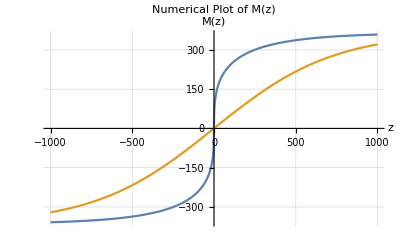

```mathematica
Plot[{ MofZ[z],MofZAppr[z]},{z,-1000,1000},PlotRange->All,PlotPoints->50,AxesLabel->{"z","M(z)"},PlotLabel->"Numerical Plot of M(z)",GridLines->Automatic]
```

```mathematica
U[z_]:=Abs[-(4 LVal^5)/(3 MofZ[z]^3)]^2
```

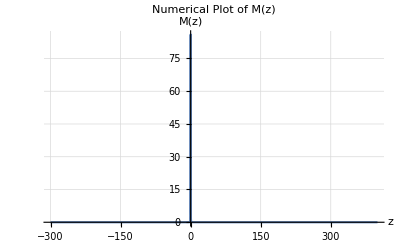

```mathematica
Plot[U[z],{z,-300,400},PlotRange->All,PlotPoints->50,AxesLabel->{"z","M(z)"},PlotLabel->"Numerical Plot of M(z)",GridLines->Automatic]
```

```mathematica
mm:=16/9 LVal^10/SubPlus[M]^6
NIntegrate[U[z]-mm, {z, -0.1, 0.1}]
```

FindRoot::nlnum: The function value {0.00500225-1. z} is not a list of numbers with dimensions {1} at {M} = {10.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[M,mVal,LVal,z]==0,{M,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.10833×10^-6}. NIntegrate obtained 427461. and 357791. for the integral and error estimates.

427461.

```mathematica
U[10000]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

7.5×10^-6